```mathematica
PiRectangles[n_]:=Module[{pi,pts,i},
pts=Table[0,{i,0,n}];
pi=Pi;
For[i=1,i≤n,i++,
pts[[i+1]]=pts[[i]]+Floor[pi]*Exp[i*ⅈ*Pi/2];
pi=10Mod[pi,1];
];
pts=Table[{Re[pts[[i]]],Im[pts[[i]]]},{i,1,n+1}];
Show[Graphics[Line[pts]]]
];
```

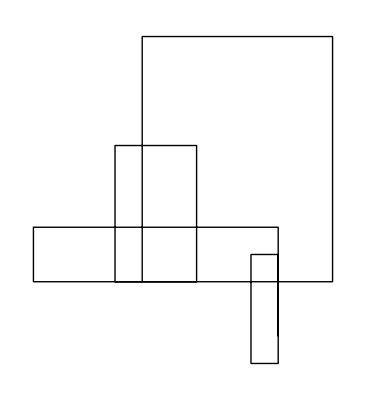

```mathematica
PiRectangles[15]
```